# Maxwell-Boltzman distribution

```mathematica
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
```

```mathematica
(*prob of speed v at temp T*)
MaxBoltzDist[T_,v_]:=PDF[MaxwellDistribution[√((kB T)/mRb)],v];

MaxBoltzSpeedSample[T_,speedband_,samples_]:=Module[
{fmax,y,v,vdomain=speedband,f=0,flist={},vlist={},ylist={},samps=0},
fmax=MaxBoltzDist[T,√((kB T)/mRb)]; 
While [samps<samples,
v = (vdomain[[2]]-vdomain[[1]])RandomReal[];
f =MaxBoltzDist[T,v];
y=fmax RandomReal[];
If[y≤f,
AppendTo[ylist,y];(*prob that y<=f is prob that speed is measured*)
AppendTo[vlist,v];(*speeds*)
AppendTo[flist,f];(*probabilities*)
samps++;
];
];
{vlist,ylist,flist}
];

MaxBoltzVelocitySample[T_,speedband_,samples_]:=Module[{velocityList={},ex,ey,ez,v,A},
For[n=1,n<samples+1,n++,
ex=2 RandomReal[]-1;
ey=2 RandomReal[]-1;
ez=2 RandomReal[]-1;
v=MaxBoltzSpeedSample[T,speedband,1][[1,1]];
A=√(ex^2+ey^2+ez^2);
AppendTo[velocityList,{ex v/A,ey v/A,ez v/A}];
];
velocityList
];
```

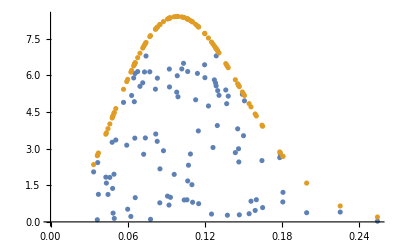

```mathematica
(*test Maxwell-Boltzmann sampling*)
{v,y,f}=MaxBoltzSpeedSample[5*^-5,{0,1},100];
ListPlot[{Transpose@{v,y},Transpose@{v,f}}]
```

```mathematica
MaxBoltzVelocitySample[5*^-5,{0,1},10]
```

{{0.0746331,-0.124351,0.049859},{-0.0435147,0.0330007,0.163811},{0.0300022,0.0210011,-0.0328762},{0.0354189,0.0433296,-0.0562395},{0.0619439,-0.0191179,-0.0529433},{0.130466,-0.106329,-0.127489},{-0.0840778,-0.0779752,-0.0668379},{-0.113374,0.0243405,-0.0398124},{0.00295118,0.13463,-0.150942},{-0.08228,-0.0691214,-0.0215349}}